# Glauber Modelling

Note that some of the functions in this notebook might have changed in the final "Geometry Averaged RAA" Notebook . I include this one since it has extra geometry stuff than the later notebook, which doesn' t need all of the functions .

Pb Parameter values for skindepth and radius (and σ_inel) obtained from arXiv:1012.1657v3 [nucl-ex]

```mathematica
aPb=208;
bPb=208;
wPb=0;
rPb=6.62;
skinDepthPb=0.546;
inelCrossSecPb=6.4;
```

### 2.2.1 Nuclear Charge Densities

#### Figure 1a: Density Distributions for nuclei used at RHIC

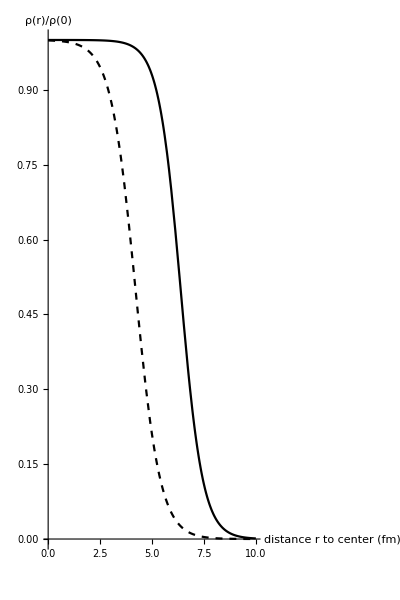

```mathematica
nucleonDensitydivRho0[r_,w_,R_,skinDepth_]:=  (1+w (r/R)^2)/(1+Exp[(r-R)/skinDepth])
Show[Plot[nucleonDensitydivRho0[r,0,6.38,0.535],{r,0,10},PlotStyle->Black,PlotLegends->Placed[{"Au"},{0.8,0.7}],AspectRatio->1.5],Plot[nucleonDensitydivRho0[r,0,4.20641,0.5977],{r,0,10},PlotStyle->{Black, Dashed},PlotLegends->Placed[{"Cu"},{0.8,0.7}],AspectRatio->1.5],AxesLabel->{"distance r to center (fm)","ρ(r)/ρ(0)"}]
```

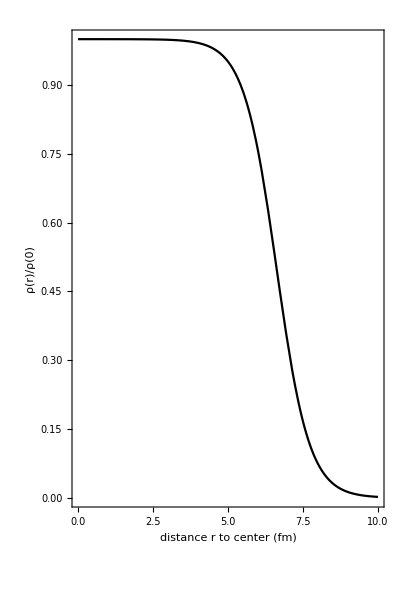

```mathematica
Show[Plot[nucleonDensitydivRho0[r,0,rPb,skinDepthPb],{r,0,10},AspectRatio->1.5,PlotStyle->Black],AxesLabel->{"distance r to center (fm)","ρ(r)/ρ(0)"},FrameLabel->{{"ρ(r)/ρ(0)",""},{"distance r to center (fm)","Normalised Nuclear Charge Density for Pb"}},Frame->True]
```

#### Figure 1b: Distribution of proton-neutron distance in the deuteron

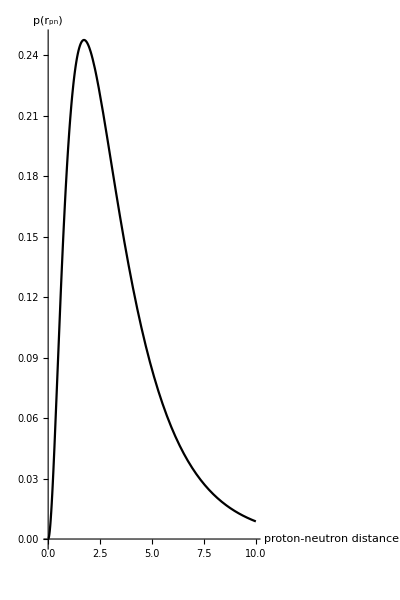

```mathematica
deuteronWaveFn[r_,a_,b_]:= 1/Sqrt[2π] Sqrt[a b (a+b)]/(b-a) (Exp[-a r]-Exp[-b r])/r 
pnDistanceDistribution[r_,a_,b_]:= 4 π r^2 deuteronWaveFn[r,a,b]^2
Plot[pnDistanceDistribution[r,0.228,1.18],{r,0,10},PlotStyle->Black,AxesLabel->{"proton-neutron distance r_pn(fm)","p(r_pn)"},PlotRange->All,AspectRatio->1.5]
```

Probability normalisation to find ρ (0) :
(Nuclear density ρ (r) a probability distribution so must integrate to 1 over all space)

```mathematica
rho0[w_,R_,skinDepth_,c_]:=rho0[w,R,skinDepth]=1/(4π NIntegrate[r^2 nucleonDensitydivRho0[r,w,R,skinDepth],{r,0,R+c*skinDepth}])
```

```mathematica
rho0[0,6.38,0.535]
```

0.000859624

Finding appropriate c value for the integration bounds (above was for upper bound of infinity)

```mathematica
rho0[0,6.38,0.535,1]
```

0.000957497

```mathematica
rho0[0,6.38,0.535,2]
```

0.000902199

```mathematica
rho0[0,6.38,0.535,3]
```

0.000877612

```mathematica
rho0[0,6.38,0.535,4]
```

0.000867112

```mathematica
rho0[0,6.38,0.535,5]
```

0.000862714

```mathematica
rho0[0,6.38,0.535,6]
```

0.000860891

```mathematica
rho0[0,6.38,0.535,7]
```

0.000860141

```mathematica
rho0[0,6.38,0.535,8]
```

0.000859834

```mathematica
rho0[0,6.38,0.535,10]
```

0.000859658

c=5 seems to be suitable, since first case where correct to 2 significant figures (rounded).

Define bound function (note this only applies when w=0)

```mathematica
bound[R_,skinDepth_,c_]:=bound[R,skinDepth,c]=R+c*skinDepth
```

```mathematica
bound[6.38,0.535,5]
```

9.055

```mathematica
bound[6.38,0.535,10]
```

11.73

I will take c = 10 to be extra safe, since the bound in this case is not very much higher

### 2.4 +2.5 Total Cross Section

#### Use equation (12) to reproduce Figure 5: Total cross section calculated in optical limit as a function of σ_inel^NN the nucleon-nucleon inelastic cross-section

To find T_AB need T_A and T_B which are defined as
 T_A(s)=Integral over z of ρ_A(sVec,z)
Where ρ_A(sVec,z) is probability per unit volume to find nucleon at location (sVec, z). In our case this is just the nuclear charge density distribution, which only depends on the scalar magnitude of the position.

```mathematica
nucleonDensity[x_,y_,z_,w_,R_,skinDepth_]:= rho0[w,R,skinDepth]  (1+w (Sqrt[x^2+y^2+z^2]/R)^2)/(1+Exp[(Sqrt[x^2+y^2+z^2]-R)/skinDepth])
```

Cole’s idea: Align b vector with y axis so that can easily make T_ABa function of the magnitude of b

Here the functions I made assume A and B have the same charge density function so T_A and T_Bare the same and I define only one function.

```mathematica
ClearAll[tAB]
```

```mathematica
t[sX_,sY_,w_,R_,skinDepth_,c_]:=2NIntegrate[nucleonDensity[sX,sY,z,w,R,skinDepth],{z,0,bound[R,skinDepth,c]},PrecisionGoal->3]
tAB[b_,w_,R_,skinDepth_,c_]:= 2 NIntegrate[t[sX,sY+b/2,w,R,skinDepth,c] t[sX,sY-b/2,w,R,skinDepth,c],{sX,0,bound[R,skinDepth,c]},{sY,-bound[R,skinDepth,c],bound[R,skinDepth,c]},PrecisionGoal->3]
```

Enter inelastic cross section in fm^2 then convert fm^2 to barns at end.

STILL NEED TO RERUN

```mathematica
totalCrossSection[a_,b_,w_,R_,skinDepth_,inelCrossSec_,c_]:= 2π NIntegrate[x (1-(1-tAB[x,w,R,skinDepth]*inelCrossSec)^(a b)),{x,0,bound[R,skinDepth,c]},PrecisionGoal->3]
```

```mathematica
inelCrossSecValues = {0.015*0.1,0.065*0.1,0.25*0.1,1*0.1,2.5*0.1,10*0.1,40*0.1}
crossSecDataLogPLot = Table[{inelCrossSec/100,totalCrossSection[197,197,0,6.38,0.535,inelCrossSec]/100},{inelCrossSec,inelCrossSecValues}]
```

{0.0015,0.0065,0.025,0.1,0.25,1.,4.}

NIntegrate::inumr: The integrand 0.000859658/(1+ⅇ^(1.86916 (-6.38+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,200}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.000015,0.511149},{0.000065,1.64022},{0.00025,3.1445},{0.001,4.43899},{0.0025,5.14907},{0.01,6.11315},{0.04,7.02223}}

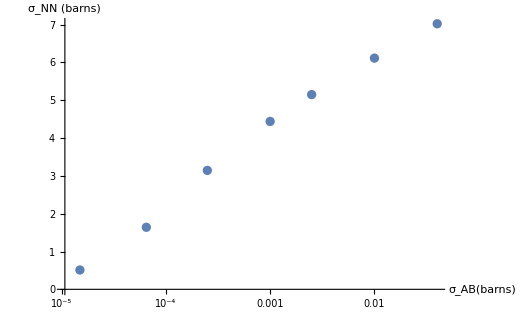

```mathematica
ListLogLinearPlot[crossSecDataLogPLot, AxesLabel->{"σ_AB(barns)","σ_NN (barns)"}]
```

### 2.3 N_coll and N_part in the optical limit approximation

#### Use equation (7) and (8) to reproduce right of Figure 5: N_coll and N_part as a function of impact parameter

```mathematica
nColl[x_,w_,R_,skinDepth_,c_,a_,b_, inelCrossSec_]:= a b tAB[x,w,R,skinDepth,c] inelCrossSec
nPart[x_,w_,R_,skinDepth_,c_,a_,b_, inelCrossSec_]:= a *2 NIntegrate[t[sX,sY,w,R,skinDepth,c] (1-(1-t[sX,sY-x,w,R,skinDepth,c]inelCrossSec)^b),{sX,0,bound[R,skinDepth,c]},{sY,-bound[R,skinDepth,c],bound[R,skinDepth,c]},PrecisionGoal->3]+b*2 NIntegrate[t[sX,sY-x,w,R,skinDepth,c] (1-(1-t[sX,sY,w,R,skinDepth,c]inelCrossSec)^a),{sX,0,bound[R,skinDepth,c]},{sY,-bound[R,skinDepth,c],bound[R,skinDepth,c]},PrecisionGoal->3]
```

```mathematica
nCollPlot=Table[{x,nColl[x,0,6.38,0.535,10,197,197,4.2]},{x,0,20,0.25}]
nPartPlot =Table[{x,nPart[x,0,6.38,0.535,10,197,197,4.2]},{x,0,20,0.25}]
```

NIntegrate::inumr: The integrand 0.000859658/(1+ⅇ^(1.86916 (-6.38+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,11.73}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.,1232.83},{0.25,1230.6},{0.5,1224.54},{0.75,1215.19},{1.,1202.3},{1.25,1186.2},{1.5,1166.9},{1.75,1144.71},{2.,1119.75},{2.25,1092.58},{2.5,1063.36},{2.75,1032.21},{3.,999.555},{3.25,965.5},{3.5,930.365},{3.75,895.079},{4.,857.029},{4.25,820.111},{4.5,782.401},{4.75,744.454},{5.,705.863},{5.25,668.63},{5.5,630.744},{5.75,592.611},{6.,555.817},{6.25,520.623},{6.5,485.122},{6.75,450.227},{7.,416.687},{7.25,383.928},{7.5,352.207},{7.75,321.761},{8.,292.561},{8.25,264.665},{8.5,238.135},{8.75,213.035},{9.,189.396},{9.25,167.247},{9.5,146.639},{9.75,127.582},{10.,110.085},{10.25,94.1394},{10.5,79.7245},{10.75,66.8639},{11.,55.4583},{11.25,45.4779},{11.5,36.8463},{11.75,29.4835},{12.,23.287},{12.25,18.1547},{12.5,13.9683},{12.75,10.6082},{13.,7.90832},{13.25,5.8937},{13.5,4.31692},{13.75,3.12762},{14.,2.2434},{14.25,1.59455},{14.5,1.12392},{14.75,0.786477},{15.,0.546242},{15.25,0.377206},{15.5,0.258884},{15.75,0.176759},{16.,0.120077},{16.25,0.0811733},{16.5,0.0546023},{16.75,0.0365549},{17.,0.0243462},{17.25,0.0161292},{17.5,0.0106254},{17.75,0.00696132},{18.,0.00453603},{18.25,0.00294108},{18.5,0.0018985},{18.75,0.00122112},{19.,0.000783224},{19.25,0.000501286},{19.5,0.000320325},{19.75,0.000204443},{20.,0.000130362}}

NIntegrate::inumr: The integrand 0.000859658/(1+ⅇ^(1.86916 (-6.38+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,11.73}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.,378.816},{0.25,378.435},{0.5,377.368},{0.75,375.579},{1.,372.866},{1.25,369.426},{1.5,365.515},{1.75,360.754},{2.,355.351},{2.25,349.289},{2.5,342.635},{2.75,335.531},{3.,327.845},{3.25,319.641},{3.5,311.086},{3.75,302.209},{4.,293.024},{4.25,282.714},{4.5,273.058},{4.75,263.025},{5.,253.035},{5.25,243.872},{5.5,233.684},{5.75,223.406},{6.,213.123},{6.25,202.868},{6.5,192.591},{6.75,181.8},{7.,172.167},{7.25,162.309},{7.5,152.438},{7.75,142.709},{8.,133.152},{8.25,123.738},{8.5,114.639},{8.75,105.76},{9.,97.1812},{9.25,88.8135},{9.5,80.772},{9.75,73.05},{10.,65.6623},{10.25,58.6607},{10.5,51.9966},{10.75,45.7229},{11.,39.8586},{11.25,34.4161},{11.5,29.4152},{11.75,24.8587},{12.,20.7563},{12.25,17.1085},{12.5,13.9097},{12.75,11.1502},{13.,8.80759},{13.25,6.85296},{13.5,5.25786},{13.75,3.9753},{14.,2.96498},{14.25,2.18372},{14.5,1.58923},{14.75,1.1442},{15.,0.815221},{15.25,0.575803},{15.5,0.403305},{15.75,0.280416},{16.,0.193675},{16.25,0.132881},{16.5,0.0906527},{16.75,0.0614865},{17.,0.0414649},{17.25,0.0278094},{17.5,0.0185432},{17.75,0.0122914},{18.,0.00809924},{18.25,0.00530538},{18.5,0.00345564},{18.75,0.00223928},{19.,0.0014447},{19.25,0.000928685},{19.5,0.000595311},{19.75,0.000380804},{20.,0.000243207}}

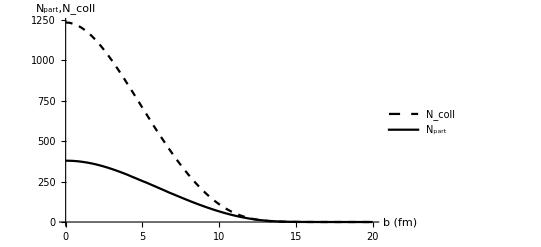

```mathematica
Show[ListPlot[nCollPlot,Joined->True,PlotStyle->{Dashed,Black},PlotLegends->{"N_coll"}],ListPlot[nPartPlot,Joined->True,PlotStyle->Black,PlotLegends->{"N_part"}],PlotRange->All,AxesLabel->{"b (fm)","N_part,N_coll"}]
```

### 3.4 Total Geometric cross section

#### Reproduce Figure 15: Total Geometric Cross section for Au+Au at √s = 200 GeV (i.e. σ_inel= 42mb)

To obtain differential cross section, take integrand of previous expression to find cross section (equivalent to integrating equation 5 with respect to b (over all b values):

```mathematica
ClearAll[diffCrossSec]
```

```mathematica
diffCrossSec[x_,w_,R_,skinDepth_,a_,b_, inelCrossSec_,c_]:= 2π x (1-(1-tAB[x,w,R,skinDepth,c]*inelCrossSec)^(a b))
```

ALSO RUN FOR Cu

```mathematica
diffCrossSecPlot=Table[{x,diffCrossSec[x,0,6.38,0.535,197,197,4.2]},{x,0,20,0.25}]
```

NIntegrate::inumr: The integrand 0.000859658/(1+ⅇ^(1.86916 (-6.38+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,200}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: 0.968253^38809 is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: 0.968304^38809 is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::munfl: 0.968448^38809 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{0.,0.},{0.25,1.5708},{0.5,3.14159},{0.75,4.71239},{1.,6.28319},{1.25,7.85398},{1.5,9.42478},{1.75,10.9956},{2.,12.5664},{2.25,14.1372},{2.5,15.708},{2.75,17.2788},{3.,18.8496},{3.25,20.4204},{3.5,21.9911},{3.75,23.5619},{4.,25.1327},{4.25,26.7035},{4.5,28.2743},{4.75,29.8451},{5.,31.4159},{5.25,32.9867},{5.5,34.5575},{5.75,36.1283},{6.,37.6991},{6.25,39.2699},{6.5,40.8407},{6.75,42.4115},{7.,43.9823},{7.25,45.5531},{7.5,47.1239},{7.75,48.6947},{8.,50.2655},{8.25,51.8363},{8.5,53.4071},{8.75,54.9779},{9.,56.5487},{9.25,58.1195},{9.5,59.6903},{9.75,61.2611},{10.,62.8319},{10.25,64.4026},{10.5,65.9734},{10.75,67.5442},{11.,69.115},{11.25,70.6858},{11.5,72.2566},{11.75,73.8274},{12.,75.3982},{12.25,76.969},{12.5,78.5397},{12.75,80.1086},{13.,81.6529},{13.25,83.0235},{13.5,83.6917},{13.75,82.6102},{14.,78.6412},{14.25,71.381},{14.5,61.5348},{14.75,50.5107},{15.,39.7334},{15.25,30.1733},{15.5,22.2929},{15.75,16.1185},{16.,11.4611},{16.25,8.0469},{16.5,5.59409},{16.75,3.85895},{17.,2.64551},{17.25,1.81118},{17.5,1.23072},{17.75,0.833984},{18.,0.563454},{18.25,0.379705},{18.5,0.255331},{18.75,0.171311},{19.,0.114723},{19.25,0.0767066},{19.5,0.0512026},{19.75,0.0341412},{20.,0.0227141}}

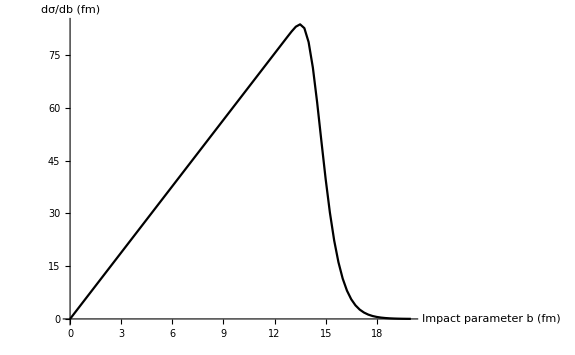

```mathematica
ListPlot[diffCrossSecPlot,Joined->True,PlotStyle->Black,AxesLabel->{"Impact parameter b (fm)","dσ/db (fm)"}]
```

```mathematica
ratioPlot=Table[{nPart[x,0,6.38,0.535,10,197,197,4.2],nColl[x,0,6.38,0.535,10,197,197,4.2]/(nPart[x,0,6.38,0.535,10,197,197,4.2])^(4/3)},{x,0.25,20,0.25}]
```

NIntegrate::inumr: The integrand 0.000859658/(1+ⅇ^(1.86916 (-6.38+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,11.73}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{378.435,0.449567},{377.368,0.449041},{375.579,0.448445},{372.866,0.447999},{369.426,0.447494},{365.515,0.446506},{360.754,0.445738},{355.351,0.444883},{349.289,0.444159},{342.635,0.443514},{335.531,0.442716},{327.845,0.442163},{319.641,0.441776},{311.086,0.441379},{302.209,0.441353},{293.024,0.440343},{282.714,0.441988},{273.058,0.441662},{263.025,0.441748},{253.035,0.441041},{243.872,0.438837},{233.684,0.438208},{223.406,0.437164},{213.123,0.436607},{202.868,0.436755},{192.591,0.436183},{181.8,0.43716},{172.167,0.435053},{162.309,0.433635},{152.438,0.432523},{142.709,0.431452},{133.152,0.430283},{123.738,0.429232},{114.639,0.42761},{105.76,0.425949},{97.1812,0.423896},{88.8135,0.422073},{80.772,0.419987},{73.05,0.417794},{65.6623,0.415565},{58.6607,0.413024},{51.9966,0.410795},{45.7229,0.40896},{39.8586,0.407321},{34.4161,0.406242},{29.4152,0.405786},{24.8587,0.406387},{20.7563,0.408239},{17.1085,0.411819},{13.9097,0.417559},{11.1502,0.425858},{8.80759,0.434785},{6.85296,0.452777},{5.25786,0.472166},{3.9753,0.496654},{2.96498,0.526677},{2.18372,0.562829},{1.58923,0.606019},{1.1442,0.65718},{0.815221,0.717273},{0.575803,0.787432},{0.403305,0.868813},{0.280416,0.963041},{0.193675,1.07159},{0.132881,1.19709},{0.0906527,1.34082},{0.0614865,1.50628},{0.0414649,1.69639},{0.0278094,1.91436},{0.0185432,2.16487},{0.0122914,2.45409},{0.00809924,2.78879},{0.00530538,3.17847},{0.00345564,3.63389},{0.00223928,4.16819},{0.0014447,4.79567},{0.000928685,5.53258},{0.000595311,6.39635},{0.000380804,7.40691},{0.000243207,8.58721}}

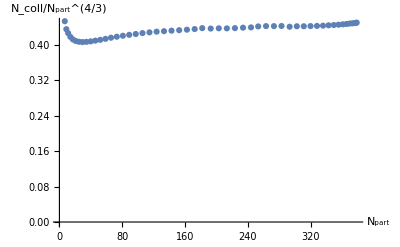

```mathematica
ListPlot[ratioPlot,AxesLabel->{"N_part","N_coll/N_part^(4/3)"},PlotRange->0.45]
```

## Performing the above for Pb+Pb

Pb Parameter values for skindepth and radius obtained from arXiv:1012.1657v3 [nucl-ex]
Value for inelastic cross section taken to be same value as before (since this was the value for RHIC, I' m assuming that' s what we should still use?)

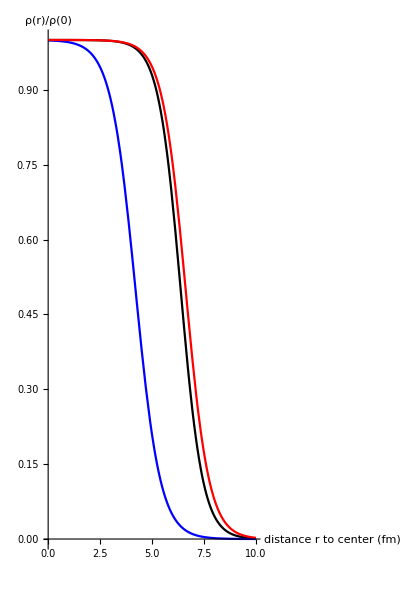

```mathematica
Show[Plot[nucleonDensitydivRho0[r,0,6.38,0.535],{r,0,10},PlotStyle->Black,PlotLegends->Placed[{"Au"},{0.8,0.7}],AspectRatio->1.5],Plot[nucleonDensitydivRho0[r,0,4.20641,0.5977],{r,0,10},PlotStyle->Blue,PlotLegends->Placed[{"Cu"},{0.8,0.7}],AspectRatio->1.5],Plot[nucleonDensitydivRho0[r,0,6.62,0.564],{r,0,10},PlotStyle->Red,PlotLegends->Placed[{"Pb"},{0.8,0.7}],AspectRatio->1.5],AxesLabel->{"distance r to center (fm)","ρ(r)/ρ(0)"}]
```

```mathematica
inelCrossSecValuesPb = {0.015*0.1,0.065*0.1,0.25*0.1,1*0.1,2.5*0.1,10*0.1,40*0.1}
crossSecDataLogPLotPb = Table[{inelCrossSec/100,totalCrossSection[208,208,0,6.62,0.564,inelCrossSec]/100},{inelCrossSec,inelCrossSecValuesPb}]
```

{0.0015,0.0065,0.025,0.1,0.25,1.,4.}

NIntegrate::inumr: The integrand 0.000767873/(1+ⅇ^(1.77305 (-6.62+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,200}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.000015,0.570094},{0.000065,1.8028},{0.00025,3.43752},{0.001,4.83209},{0.0025,5.60256},{0.01,6.65385},{0.04,7.64943}}

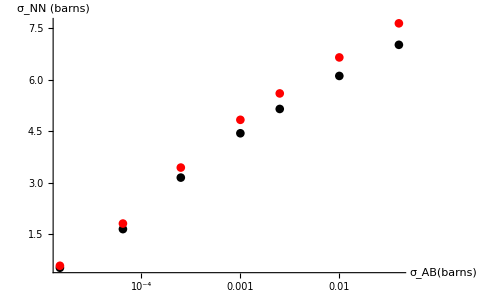

```mathematica
Show[ListLogLinearPlot[crossSecDataLogPLot,PlotStyle->Black,PlotLegends->Placed[{"Au"},{0.2,0.7}]],ListLogLinearPlot[crossSecDataLogPLotPb,PlotStyle->Red, PlotLegends->Placed[{"Pb"},{0.2,0.7}]], AxesLabel->{"σ_AB(barns)","σ_NN (barns)"},PlotRange->All]
```

```mathematica
nCollPlotPb=Table[{x,nColl[x,0,6.62,0.564,10,208,208,4.2]},{x,0,20,0.25}]
nPartPlotPb =Table[{x,nPart[x,0,6.62,0.564,10,208,208,4.2]},{x,0,20,0.25}]
```

NIntegrate::inumr: The integrand 0.000767873/(1+ⅇ^(1.77305 (-6.62+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,12.26}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.,1271.17},{0.25,1269.06},{0.5,1263.28},{0.75,1254.38},{1.,1242.35},{1.25,1226.86},{1.5,1208.37},{1.75,1186.86},{2.,1162.95},{2.25,1136.75},{2.5,1108.52},{2.75,1078.32},{3.,1046.6},{3.25,1013.44},{3.5,979.108},{3.75,943.808},{4.,907.674},{4.25,871.286},{4.5,834.483},{4.75,796.168},{5.,758.392},{5.25,720.995},{5.5,683.203},{5.75,645.671},{6.,607.913},{6.25,571.408},{6.5,536.261},{6.75,501.191},{7.,466.511},{7.25,433.141},{7.5,400.298},{7.75,368.779},{8.,338.394},{8.25,309.124},{8.5,281.09},{8.75,254.349},{9.,228.962},{9.25,204.952},{9.5,182.37},{9.75,161.231},{10.,141.576},{10.25,123.409},{10.5,106.732},{10.75,91.5284},{11.,77.8043},{11.25,65.5066},{11.5,54.6063},{11.75,45.0431},{12.,36.7467},{12.25,29.6408},{12.5,23.6287},{12.75,18.616},{13.,14.4929},{13.25,11.1533},{13.5,8.48608},{13.75,6.38634},{14.,4.756},{14.25,3.50864},{14.5,2.56428},{14.75,1.85855},{15.,1.33677},{15.25,0.955117},{15.5,0.677555},{15.75,0.478044},{16.,0.33552},{16.25,0.234241},{16.5,0.162793},{16.75,0.112628},{17.,0.0775874},{17.25,0.0532064},{17.5,0.0363314},{17.75,0.0246914},{18.,0.0167003},{18.25,0.0112389},{18.5,0.00752566},{18.75,0.0050146},{19.,0.00332622},{19.25,0.00219748},{19.5,0.00144694},{19.75,0.000950194},{20.,0.000622693}}

NIntegrate::inumr: The integrand 0.000767873/(1+ⅇ^(1.77305 (-6.62+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,12.26}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.,399.256},{0.25,398.957},{0.5,397.834},{0.75,396.021},{1.,394.194},{1.25,390.372},{1.5,386.213},{1.75,381.752},{2.,376.469},{2.25,370.399},{2.5,363.886},{2.75,356.798},{3.,349.215},{3.25,341.123},{3.5,332.735},{3.75,323.915},{4.,314.773},{4.25,305.351},{4.5,295.018},{4.75,284.989},{5.,274.862},{5.25,264.599},{5.5,255.183},{5.75,244.891},{6.,234.476},{6.25,224.038},{6.5,213.61},{6.75,203.203},{7.,192.425},{7.25,182.076},{7.5,172.361},{7.75,162.409},{8.,152.507},{8.25,142.765},{8.5,133.157},{8.75,123.854},{9.,114.759},{9.25,105.945},{9.5,97.3463},{9.75,89.0595},{10.,81.0688},{10.25,73.416},{10.5,66.0833},{10.75,59.1152},{11.,52.5073},{11.25,46.2834},{11.5,40.4665},{11.75,35.0683},{12.,30.0985},{12.25,25.5664},{12.5,21.4775},{12.75,17.8285},{13.,14.6201},{13.25,11.8331},{13.5,9.45513},{13.75,7.45357},{14.,5.79756},{14.25,4.4544},{14.5,3.37937},{14.75,2.5341},{15.,1.87953},{15.25,1.38027},{15.5,1.00445},{15.75,0.724621},{16.,0.518922},{16.25,0.368823},{16.5,0.260545},{16.75,0.182995},{17.,0.12779},{17.25,0.0887781},{17.5,0.0613628},{17.75,0.0421939},{18.,0.0288688},{18.25,0.0196481},{18.5,0.0133017},{18.75,0.00895738},{19.,0.00600007},{19.25,0.00399836},{19.5,0.00265182},{19.75,0.00175165},{20.,0.00115305}}

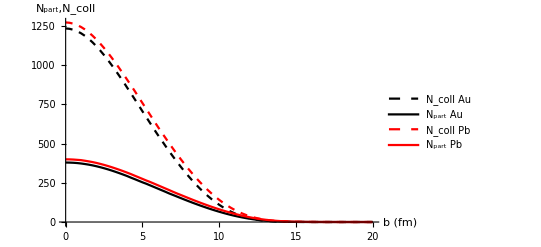

```mathematica
Show[ListPlot[nCollPlot,Joined->True,PlotStyle->{Dashed,Black},PlotLegends->{"N_coll Au"}],ListPlot[nPartPlot,Joined->True,PlotStyle->Black,PlotLegends->{"N_part Au"}],ListPlot[nCollPlotPb,Joined->True,PlotStyle->{Dashed,Red},PlotLegends->{"N_coll Pb"}],ListPlot[nPartPlotPb,Joined->True,PlotStyle->Red,PlotLegends->{"N_part Pb"}],PlotRange->All,AxesLabel->{"b (fm)","N_part,N_coll"}]
```

```mathematica
diffCrossSecPlotPb=Table[{x,diffCrossSec[x,0,6.62,0.564,208,208,4.2]},{x,0,20,0.25}]
```

NIntegrate::inumr: The integrand 0.000767873/(1+ⅇ^(1.77305 (-6.62+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,200}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

General::munfl: 0.970634^43264 is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: 0.970674^43264 is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: 0.9708^43264 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.,0.},{0.25,1.5708},{0.5,3.14159},{0.75,4.71239},{1.,6.28319},{1.25,7.85398},{1.5,9.42478},{1.75,10.9956},{2.,12.5664},{2.25,14.1372},{2.5,15.708},{2.75,17.2788},{3.,18.8496},{3.25,20.4204},{3.5,21.9911},{3.75,23.5619},{4.,25.1327},{4.25,26.7035},{4.5,28.2743},{4.75,29.8451},{5.,31.4159},{5.25,32.9867},{5.5,34.5575},{5.75,36.1283},{6.,37.6991},{6.25,39.2699},{6.5,40.8407},{6.75,42.4115},{7.,43.9823},{7.25,45.5531},{7.5,47.1239},{7.75,48.6947},{8.,50.2655},{8.25,51.8363},{8.5,53.4071},{8.75,54.9779},{9.,56.5487},{9.25,58.1195},{9.5,59.6903},{9.75,61.2611},{10.,62.8319},{10.25,64.4026},{10.5,65.9734},{10.75,67.5442},{11.,69.115},{11.25,70.6858},{11.5,72.2566},{11.75,73.8274},{12.,75.3982},{12.25,76.969},{12.5,78.5398},{12.75,80.1106},{13.,81.6814},{13.25,83.251},{13.5,84.8057},{13.75,86.2485},{14.,87.2101},{14.25,86.8583},{14.5,84.1063},{14.75,78.2542},{15.,69.5288},{15.25,58.9808},{15.5,47.9868},{15.75,37.6737},{16.,28.7275},{16.25,21.4231},{16.5,15.7172},{16.75,11.3193},{17.,8.06069},{17.25,5.70088},{17.5,4.02056},{17.75,2.81166},{18.,1.95777},{18.25,1.35809},{18.5,0.939223},{18.75,0.647894},{19.,0.445781},{19.25,0.306077},{19.5,0.209767},{19.75,0.143537},{20.,0.0980504}}

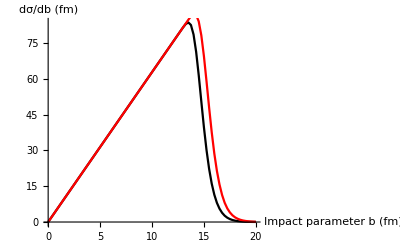

```mathematica
Show[ListPlot[diffCrossSecPlot,Joined->True,PlotStyle->Black,PlotLegends->Placed[{"Au"},{0.2,0.7}]],ListPlot[diffCrossSecPlotPb,Joined->True,PlotStyle->Red,PlotLegends->Placed[{"Pb"},{0.2,0.7}]],AxesLabel->{"Impact parameter b (fm)","dσ/db (fm)"}]
```

```mathematica
diffCrossSecPlotCu=Table[{x,diffCrossSec[x,0,4.20641,0.5977,63,63,4.2]},{x,0,20,0.25}]
```

NIntegrate::inumr: The integrand 0.00267457/(1+ⅇ^(1.67308 (-4.20641+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,200}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.,0.},{0.25,1.5708},{0.5,3.14159},{0.75,4.71239},{1.,6.28319},{1.25,7.85398},{1.5,9.42478},{1.75,10.9956},{2.,12.5664},{2.25,14.1372},{2.5,15.708},{2.75,17.2788},{3.,18.8496},{3.25,20.4204},{3.5,21.9911},{3.75,23.5619},{4.,25.1327},{4.25,26.7035},{4.5,28.2743},{4.75,29.8451},{5.,31.4159},{5.25,32.9867},{5.5,34.5575},{5.75,36.1283},{6.,37.6991},{6.25,39.2699},{6.5,40.8407},{6.75,42.4115},{7.,43.9823},{7.25,45.5531},{7.5,47.1239},{7.75,48.6947},{8.,50.265},{8.25,51.831},{8.5,53.3686},{8.75,54.7823},{9.,55.8188},{9.25,56.0277},{9.5,54.8794},{9.75,52.0225},{10.,47.498},{10.25,41.7301},{10.5,35.3578},{10.75,29.0142},{11.,23.1613},{11.25,18.0735},{11.5,13.8449},{11.75,10.448},{12.,7.7906},{12.25,5.75262},{12.5,4.21427},{12.75,3.06748},{13.,2.22093},{13.25,1.60076},{13.5,1.14911},{13.75,0.822271},{14.,0.587157},{14.25,0.417923},{14.5,0.296727},{14.75,0.210251},{15.,0.148687},{15.25,0.104957},{15.5,0.0739632},{15.75,0.0520388},{16.,0.0365577},{16.25,0.0256498},{16.5,0.0179708},{16.75,0.0125714},{17.,0.00878592},{17.25,0.00613338},{17.5,0.00427694},{17.75,0.00297845},{18.,0.00207232},{18.25,0.00144041},{18.5,0.0010003},{18.75,0.000693962},{19.,0.000481016},{19.25,0.000333146},{19.5,0.000230542},{19.75,0.000159422},{20.,0.000110134}}

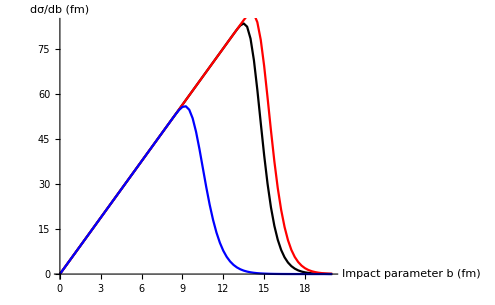

```mathematica
Show[ListPlot[diffCrossSecPlot,Joined->True,PlotStyle->Black,PlotLegends->Placed[{"Au"},{0.2,0.7}]],ListPlot[diffCrossSecPlotPb,Joined->True,PlotStyle->Red,PlotLegends->Placed[{"Pb"},{0.2,0.7}]],ListPlot[diffCrossSecPlotCu,Joined->True,PlotStyle->Blue,PlotLegends->Placed[{"Cu"},{0.2,0.7}]],AxesLabel->{"Impact parameter b (fm)","dσ/db (fm)"}]
```

## Performing the above for Pb+Pb at LHC with σ_inel^NN= 64mb

Pb Parameter values for skindepth and radius obtained from 
Value for inelastic cross section taken to be same value as before (since this was the value for RHIC, I' m assuming that' s what we should still use?)

```mathematica
nCollPlotPbLHC=Table[{x,nColl[x,0,6.62,0.564,10,208,208,6.4]},{x,0,20,0.25}]
nPartPlotPbLHC =Table[{x,nPart[x,0,6.62,0.564,10,208,208,6.4]},{x,0,20,0.25}]
```

NIntegrate::inumr: The integrand 0.000767873/(1+ⅇ^(1.77305 (-6.62+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,12.26}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.,1937.03},{0.25,1933.8},{0.5,1925.},{0.75,1911.44},{1.,1893.1},{1.25,1869.51},{1.5,1841.33},{1.75,1808.55},{2.,1772.12},{2.25,1732.19},{2.5,1689.17},{2.75,1643.16},{3.,1594.82},{3.25,1544.28},{3.5,1491.97},{3.75,1438.18},{4.,1383.12},{4.25,1327.67},{4.5,1271.59},{4.75,1213.21},{5.,1155.64},{5.25,1098.66},{5.5,1041.07},{5.75,983.879},{6.,926.344},{6.25,870.717},{6.5,817.159},{6.75,763.72},{7.,710.873},{7.25,660.025},{7.5,609.978},{7.75,561.949},{8.,515.648},{8.25,471.047},{8.5,428.328},{8.75,387.58},{9.,348.894},{9.25,312.308},{9.5,277.897},{9.75,245.685},{10.,215.735},{10.25,188.052},{10.5,162.639},{10.75,139.472},{11.,118.559},{11.25,99.8196},{11.5,83.2096},{11.75,68.6371},{12.,55.995},{12.25,45.167},{12.5,36.0056},{12.75,28.3672},{13.,22.0844},{13.25,16.9955},{13.5,12.9312},{13.75,9.73157},{14.,7.24724},{14.25,5.3465},{14.5,3.90747},{14.75,2.83208},{15.,2.03698},{15.25,1.45542},{15.5,1.03247},{15.75,0.728447},{16.,0.511268},{16.25,0.356939},{16.5,0.248066},{16.75,0.171624},{17.,0.118228},{17.25,0.0810764},{17.5,0.0553621},{17.75,0.037625},{18.,0.025448},{18.25,0.0171259},{18.5,0.0114677},{18.75,0.0076413},{19.,0.00506853},{19.25,0.00334855},{19.5,0.00220486},{19.75,0.00144791},{20.,0.000948866}}

NIntegrate::inumr: The integrand 0.000767873/(1+ⅇ^(1.77305 (-6.62+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,12.26}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.,405.687},{0.25,405.408},{0.5,404.567},{0.75,403.18},{1.,401.15},{1.25,398.429},{1.5,395.094},{1.75,390.942},{2.,386.383},{2.25,381.078},{2.5,375.16},{2.75,363.1},{3.,361.492},{3.25,353.937},{3.5,345.907},{3.75,337.46},{4.,328.641},{4.25,319.48},{4.5,310.038},{4.75,299.074},{5.,290.386},{5.25,280.283},{5.5,270.021},{5.75,259.531},{6.,249.189},{6.25,238.683},{6.5,228.156},{6.75,217.381},{7.,206.908},{7.25,196.634},{7.5,186.246},{7.75,175.99},{8.,165.811},{8.25,155.775},{8.5,145.902},{8.75,136.132},{9.,126.673},{9.25,117.454},{9.5,108.415},{9.75,99.7323},{10.,91.3071},{10.25,83.1555},{10.5,75.3244},{10.75,67.8366},{11.,60.7332},{11.25,53.9618},{11.5,47.5927},{11.75,41.6417},{12.,36.0988},{12.25,30.9924},{12.5,26.3277},{12.75,22.1161},{13.,18.3563},{13.25,15.0437},{13.5,12.1682},{13.75,9.7099},{14.,7.6455},{14.25,5.93998},{14.5,4.55606},{14.75,3.45017},{15.,2.5837},{15.25,1.91344},{15.5,1.4028},{15.75,1.01906},{16.,0.734049},{16.25,0.524903},{16.5,0.372509},{16.75,0.262734},{17.,0.184198},{17.25,0.128427},{17.5,0.0890532},{17.75,0.061423},{18.,0.0421389},{18.25,0.0287615},{18.5,0.019525},{18.75,0.0131841},{19.,0.00885594},{19.25,0.00591828},{19.5,0.00393553},{19.75,0.00260535},{20.,0.00171827}}

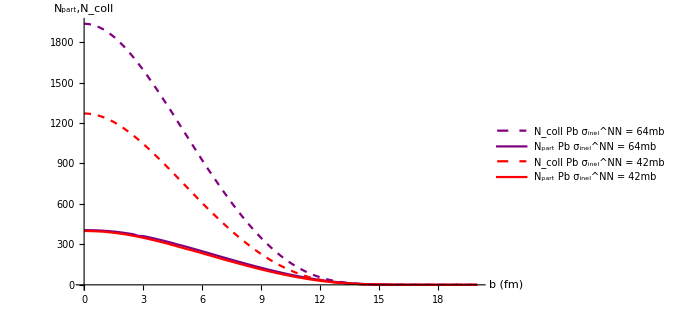

```mathematica
Show[ListPlot[nCollPlotPbLHC,Joined->True,PlotStyle->{Dashed,Purple},PlotLegends->{"N_coll Pb σ_inel^NN = 64mb"}],ListPlot[nPartPlotPbLHC,Joined->True,PlotStyle->Purple,PlotLegends->{"N_part Pb σ_inel^NN = 64mb"}],ListPlot[nCollPlotPb,Joined->True,PlotStyle->{Dashed,Red},PlotLegends->{"N_coll Pb σ_inel^NN = 42mb"}],ListPlot[nPartPlotPb,Joined->True,PlotStyle->Red,PlotLegends->{"N_part Pb σ_inel^NN = 42mb"}],PlotRange->All,AxesLabel->{"b (fm)","N_part,N_coll"}]
```

```mathematica
diffCrossSecPlotPbLHC=Table[{x,diffCrossSec[x,0,6.62,0.564,208,208,6.4,10]},{x,0,20,0.25}]
```

NIntegrate::inumr: The integrand 0.000767873/(1+ⅇ^(1.77305 (-6.62+√Plus[«3»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,12.26}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

General::munfl: 0.955228^43264 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.955291^43264 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.955493^43264 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

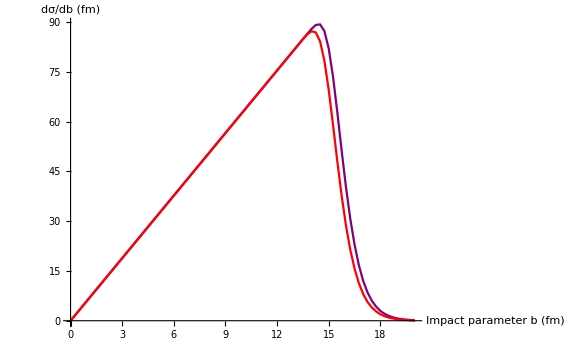

```mathematica
Show[ListPlot[diffCrossSecPlotPbLHC,Joined->True,PlotStyle->Purple,PlotLegends->Placed[{"Pb σ_inel^NN = 64mb"},{0.2,0.7}]],ListPlot[diffCrossSecPlotPb,Joined->True,PlotStyle->Red,PlotLegends->Placed[{"Pb σ_inel^NN = 42mb"},{0.2,0.7}]],AxesLabel->{"Impact parameter b (fm)","dσ/db (fm)"}]
```

### Extra stuff (not finished since not actually needed for geom RAA)

Could then also find the quantities N_coll and N_partat the impact parameters which determine the bounds of the centrality class to characterise the classes in this way.

Can find the mean of these quantities for each centrality class . For the definitions of functions to find such means below, accuracy determined by step size used in table .

```mathematica
meanNPart[w_,R_,skinDepth_,a_,b_, inelCrossSec_,c_,fractionUpper_ fractionLower_,stepSize_]:=
meanNPart[w,R,skinDepth,a,b, inelCrossSec,c,fractionUpper,fractionLower,stepSize]=
Mean[Table[nPart[x,w,R,skinDepth,c,a,b, inelCrossSec],{x,centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower],centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower],stepSize}]]
```

```mathematica
meanNColl[w_,R_,skinDepth_,a_,b_, inelCrossSec_,c_,fractionUpper_ fractionLower_,stepSize_]:=
meanNColl[w,R,skinDepth,a,b, inelCrossSec,c,fractionUpper,fractionLower,stepSize]=
Mean[Table[nColl[x,w,R,skinDepth,c,a,b, inelCrossSec],{x,centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower],centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower],stepSize}]]
```

Another way to find a kind of averages of these quantities, which seems to be weighted by differential cross-section evaluated at each impact parameter within the centrality class

```mathematica
nPartCentrality[w_,R_,skinDepth_,a_,b_, inelCrossSec_,c_,fractionUpper_ fractionLower_,stepSize_]:=
nPartCentrality[w,R,skinDepth,a,b, inelCrossSec,c,fractionUpper,fractionLower,stepSize]=
NIntegrate[nPart[x,w,R,skinDepth,c,a,b, inelCrossSec] diffCrossSec[x,w,R,skinDepth,a,b, inelCrossSec,c],{x,centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower],centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower]}]/NIntegrate[ diffCrossSec[x,w,R,skinDepth,a,b, inelCrossSec,c],{x,centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower],centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower]}]
```

```mathematica
nCollCentrality[w_,R_,skinDepth_,a_,b_, inelCrossSec_,c_,fractionUpper_ fractionLower_,stepSize_]:=
nCollCentrality[w,R,skinDepth,a,b, inelCrossSec,c,fractionUpper,fractionLower,stepSize]=
NIntegrate[nColl[x,w,R,skinDepth,c,a,b, inelCrossSec] diffCrossSec[x,w,R,skinDepth,a,b, inelCrossSec,c],{x,centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower],centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower]}]/NIntegrate[ diffCrossSec[x,w,R,skinDepth,a,b, inelCrossSec,c],{x,centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower],centralityClassUpperBound[w,R,skinDepth,a,b, inelCrossSec,c,fractionLower]}]
```